## Basic Definitions (Key)

```mathematica
ClearAll["Global`*"];
```

#### Integrand

```mathematica
Tuv=1/4((4 v^2-(1+v^2-u^2)^2)/(4u v))^2((u^2+v^2-3)/(2u v))^2((-2+(u^2+v^2-3)/(2 u v)Log[Abs[(3-(u+v)^2)/(3-(u-v)^2)]])^2+π^2((u^2+v^2-3)/(2 u v))^2 HeavisideTheta[u+v-√3])/.{u->#1,v->#2}&;
(*FullSimplify[Tuv[(s+t)/(√2),(s-t)/(√2)],Assumptions->s>0&&t<1&&t>-1];*)
(*Tst=Evaluate[%/.{s->#1,t->#2}]&;*)
```

#### Momentum as arrays

```mathematica
(*Define parameters. kmax is determined by Subaru-HSC events, which gives fmax=3Hz(M/10^16g)^(-1/2)=(1~2)×10^-5 Hz. kmax=fmax*2π. fmax=kmax/(2π)=(1~2)×10^-5 Hz.
fmin is given by PTA constraint. For 5 bins, we choose 10^-8 Hz as fmin, which is 3.17×10^-8 Hz.
Then, we normalize k by kmax=k2, and use wid=k2/k1=f2/f1=(1~2)×10^3 as a parameter.  *)
```

```mathematica
karray=Array[10^(-5+0.02(#-1))&,301];
wid=10^3;
k2=1;
k1=k2/wid;
A=1.;
```

#### Parallel calculation

```mathematica
nKernels=Min[8,$ProcessorCount];
LaunchKernels[nKernels];
```

#### Integrate

```mathematica
Method->"LocalAdaptive";
GWarray=ParallelArray[NIntegrate[3 Tuv[u,v]/(u^2 v^2),{v,1/(wid karray[[#]]),1/karray[[#]]},{u,Max[Abs[1-v],1/(wid karray[[#]])],Min[1+v,1/karray[[#]]]},PrecisionGoal->10,WorkingPrecision->20]&,Length[karray]]//Quiet;
```

```mathematica
data=Transpose[{karray,GWarray}];
Export["GWarray_results.csv",data,"CSV"];
```

#### Import

```mathematica
Directory[]
```

/Users/SPi

```mathematica
(*如果存为 CSV 且无表头*)
SetDirectory[NotebookDirectory[]];
data=Import["GWarray_results.csv","CSV"];
kappa=data[[All,1]];
omega=data[[All,2]];(*如果存为纯文本两列表格（.dat/.txt）*)(*data=Import["GWarray_results.dat","Table"];*)
```

```mathematica
data[[1]]
```

{0.00001,0.0000206569503724535824}

#### Relativistic DOF

final g(f_min): 10.75

initial g(f_max): 106.75

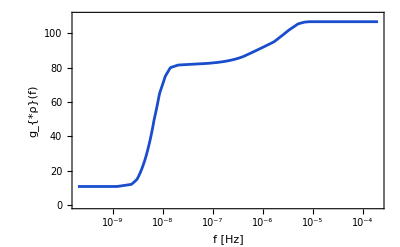

```mathematica
ClearAll[farray,resultGofF,rawGData,denseGInterp];


rawGData=Join[Table[{t,3.36},{t,10^-8,10^-5,10^-6}],{{10^-4,3.38},{5*^-4,7.5},{10^-3,10.70}},Table[{t,10.75},{t,2*^-3,0.05,0.01}],{{0.08,12.0},{0.1,15.0},{0.12,22.0},{0.15,35.0},{0.18,50.0},{0.22,65.0},{0.28,75.0},{0.35,80.0},{0.5,81.5}},Table[{t,82.0+(t-1)*0.5},{t,1,10,1}],{{40.0,95.0},{80.0,102.0},{120.0,105.5},{160.0,106.5},{200.0,106.75}},Table[{t,106.75},{t,500,10^7,1000}]];
resultGofF=Module[{mpl=1.2209*10^19,t0=2.348*10^-13,gs0=3.909,hzConv=2.418*10^24,gTInterp,freqFunc,bigTable,fToGInterp},gTInterp=Interpolation[Map[{Log10[#[[1]]],Log10[#[[2]]]}&,rawGData],InterpolationOrder->1];
freqFunc[temp_]:=Module[{g},g=10^gTInterp[Log10[temp]];
(1/(2 Pi))*(gs0/g)^(1/3)*(t0/temp)*(1.66*Sqrt[g]*temp^2/mpl)*hzConv];
bigTable=Table[{Log10[freqFunc[t]],gTInterp[Log10[t]]},{t,10^Range[-7,7,0.005]}];
fToGInterp=Interpolation[bigTable,InterpolationOrder->1];
farray=2*10^-5*Array[10^(-5+0.02 (#-1))&,301];
Map[10^fToGInterp[Log10[#]]&,farray]];
Print["final g(f_min): ",First[resultGofF]];
Print["initial g(f_max): ",Last[resultGofF]];
ListLogLinearPlot[Transpose[{farray,resultGofF}],Joined->True,Frame->True,PlotRange->{{Min[farray],Max[farray]},{0,110}},FrameLabel->{"f [Hz]","g_{*ρ}(f)"},PlotStyle->{RGBColor[0.1,0.3,0.8],Thickness[0.005]},GridLines->Automatic]
```

#### Plot

```mathematica
(*Define the style first for cleaner code*)
gwSignalStyle1=Directive[Blue,AbsoluteThickness[4],JoinForm["Round"],Opacity[1]];
gwSignalStyle2=Directive[Black,AbsoluteThickness[4],JoinForm["Round"],Opacity[1]];
(*Usage inside your Plot/ListLogLogPlot*)
(*Assuming'gwModelData' is your {freq,omega} list*)
```

```mathematica
(*The integral is done for κ=k/Subscript[k, max]=f/Subscript[f, max].*)
```

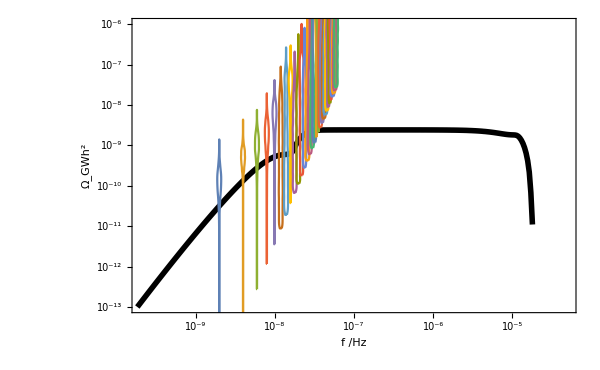

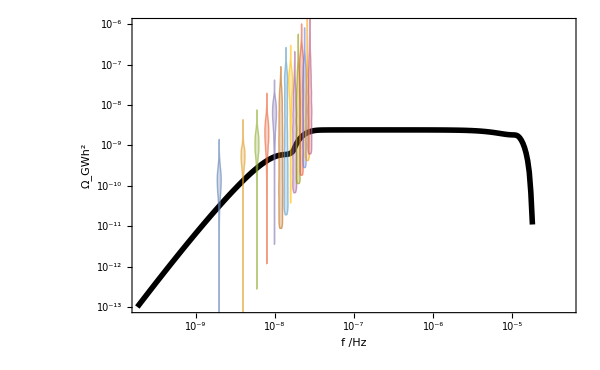

```mathematica
Azeta=1.35532 10^-2;
IGW1=ListLogLogPlot[Array[{1.5 10^-5 karray[[#]],1.6 10^-5 Azeta^2 omega[[#]]}&,Length[karray]],PlotRange->{{2 10^-10,5 10^-5},{10^-13,10^-6}},Joined->True,Frame->True,PlotStyle->gwSignalStyle2,BaseStyle->FontSize->18,FrameStyle->FontFamily->"Times",LabelStyle->GrayLevel[0],Axes->False,ImageSize->600,GridLines->Automatic,FrameLabel->{f"/Hz","Ω_GWh^2"}];
Show[IGW1,PTA1]
Show[PTA14,IGW1]
```

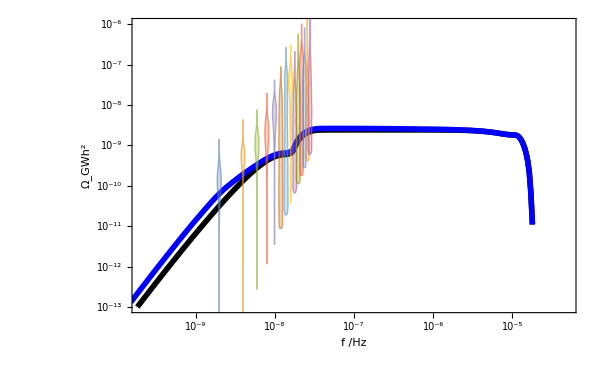

```mathematica
IGW2=ListLogLogPlot[Array[{1.5 10^-5 karray[[#]],1.6 10^-5 (Azeta)^2(resultGofF[[#]]/106.75)^(-1/3)omega[[#]]}&,Length[karray]],PlotRange->{{2 10^-10,5 10^-5},{10^-13,10^-6}},Joined->True,Frame->True,PlotStyle->gwSignalStyle1,BaseStyle->FontSize->18,FrameStyle->FontFamily->"Times",LabelStyle->GrayLevel[0],Axes->False,ImageSize->600,GridLines->Automatic,FrameLabel->{f"/Hz","Ω_GW"}];
Show[PTA14,IGW1,IGW2]
```